# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]][[1;;-1]]
```

{D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

```mathematica
data=Map[{#[[1]]*10^(-6), #[[2]]*10^5, #[[3]]}&,data,{2}];
```

## Plotting

{Gas, Gemischt, Flüssig}

```mathematica
colours={RGBColor[0,0.6,0], RGBColor[0.56,0.37,0.60],Blue}
```

{RGBColor[0, 0.6, 0],RGBColor[0.56, 0.37, 0.6],RGBColor[0, 0, 1]}

```mathematica
states={"Gas", "Gemischt","Flüssig"}
```

{Gas,Gemischt,Flüssig}

```mathematica
assoc=AssociationThread[states,colours];
```

```mathematica
cf[_,_,_]=Black;
```

```mathematica
Do[((cf[i,x_,y_]/;(x-#[[1]])^2+(y-#[[2]])^2<=0.01=assoc[#[[3]]])&)/@data[[i]],{i,1,Length[data]}]
```

```mathematica
(*Do[cf[data[[i,j,1]],data[[i,j,2]]]=assoc[data[[i,j,3]]],{i,1,Length[data]},{j,1,Length[data[[i]]]}]*)
```

{Around[#[[1]],σv],Around[#[[2]],σP]} for error bars

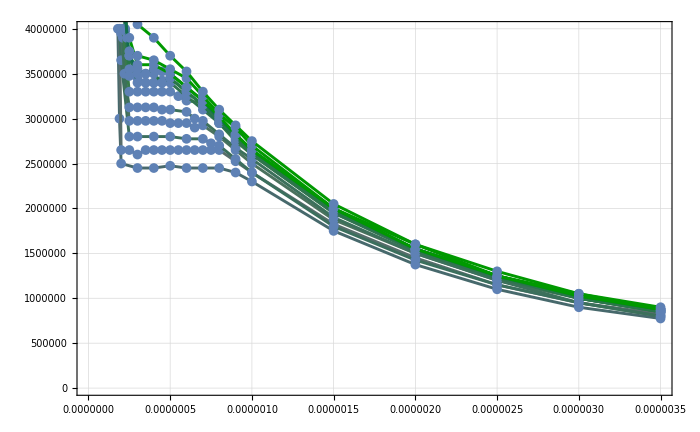

```mathematica
plts=Flatten@Table[{ListPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,Joined->True,pltsettings,PlotStyle->Thickness[0.003]],ListPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,PlotStyle->PointSize[0.01]]},{i,1,Length[data]}];
Show[plts]
```

## This is the final plot

```mathematica
(*plotMarkers->{Graphics[{Disk[{0,0},Scaled[0.02]]}],Graphics[{Disk[{0,0},Scaled[0.02]]}] }*)
```

```mathematica
plotMarkers=Charting`CommonDump`GraphicsOpenPlotMarkers[][[1;;3]];
```

```mathematica
plotMarkerAssoc=AssociationThread[states,plotMarkers];
```

```mathematica
flattened=Flatten[Map[#[[1;;3]]&, data,{2}],1];
```

```mathematica
pmarkers=plotMarkerAssoc[#[[3]]]&/@flattened;
```

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

```mathematica
pcolours=Flatten[Table[ConstantArray[cols[[i]],Length[data[[i]]]],{i,1,Length[data]}],1];
```

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours]]
```

-Graphics-

## Fitting

```mathematica
R=8.314;
```

```mathematica
a0=0.8405;
b0=9.397/10^5;
n0=1.330/10^3;
```

```mathematica
a0=7.857/10;
b0=0.0879/1000;
n0=1.330/10^3;
```

```mathematica
temps[[-4]]
```

45.6

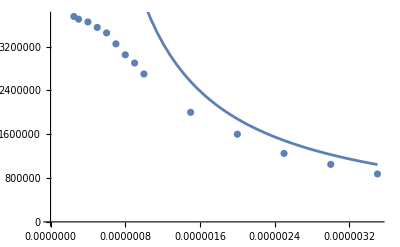

```mathematica
Show[ListPlot[{#[[1]],#[[2]]}&/@data[[-2]]], Plot[(n0 R (temps⟦-2⟧+273.15))/(V-n0 b0)-(n0^2 a0)/V,{V,0,3.5*10^(-6)}]]
```

```mathematica
fit=Table[NonlinearModelFit[({#1⟦1⟧,#1⟦2⟧}&)/@data⟦i⟧,(n R (temps⟦i⟧+273.15))/(V-n b)-(n^2 a)/V^2,{{a,0.8405},{b,9.397/10^5},{n,1.330/10^3}},V],{i,-4,-1}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
cols2=ColorData["ThermometerColors"]/@Rescale[temps[[-4;;-1]]];
```

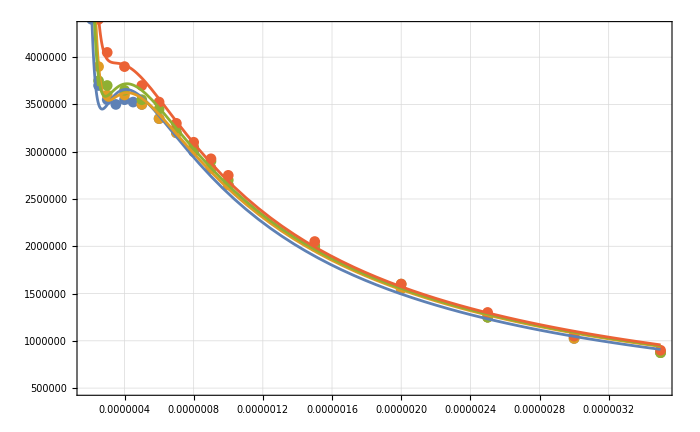

```mathematica
Show[ListPlot[data[[-4;;-1,All,{1,2}]]],Plot[Evaluate[#[t]&/@fit],{t,1.5*10^(-7),3.5*10^(-6)}],PlotRange->{All,{0.5*10^6,4.3*10^6}},pltsettings]
```

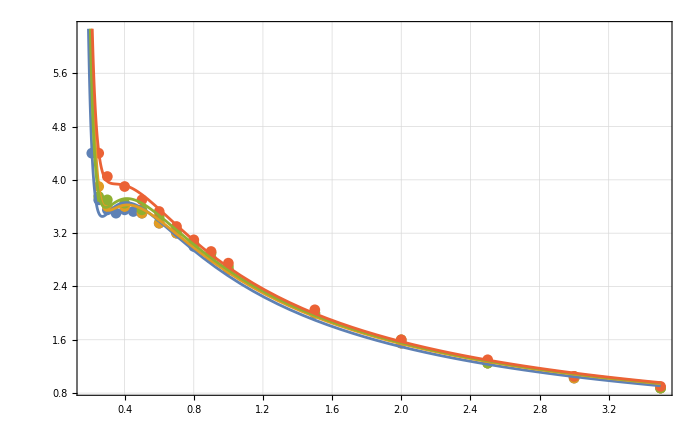

```mathematica
Show[ListPlot[Map[{#[[1]]*10^6,#[[2]]*10^(-6)}&,data[[-4;;-1,All,{1,2}]],{2}]],Plot[Evaluate[10^(-6)#[t*10^(-6)]&/@fit],{t,0,3.5}],PlotRange->{All,{Automatic,4.3}},pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/fig3.pdf",Show[ListPlot[Map[{#[[1]]*10^6,#[[2]]*10^(-6)}&,data[[-4;;-1,All,{1,2}]],{2}]],Plot[Evaluate[10^(-6)#[t*10^(-6)]&/@fit],{t,0,3.5}],PlotRange->{All,{Automatic,4.3}},pltsettings],Background->None];
```

```mathematica
temps
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
partable=#["ParameterTableEntries"]&/@fit
```

{{{0.775361,0.00783414,98.972,2.52801×10^-21},{0.0000840041,1.03061×10^-6,81.5089,3.81201×10^-20},{0.00130071,0.0000209549,62.072,1.7106×10^-18}},{{0.798833,0.00586501,136.203,4.18483×10^-19},{0.0000876329,7.19746×10^-7,121.755,1.43563×10^-18},{0.00135084,0.0000139921,96.5435,1.83863×10^-17}},{{0.777354,0.00829007,93.7692,2.53294×10^-17},{0.0000845,1.03618×10^-6,81.5499,1.17421×10^-16},{0.00135315,0.0000189304,71.4802,4.99185×10^-16}},{{0.779038,0.00648849,120.065,1.67417×10^-18},{0.0000861257,7.88025×10^-7,109.293,4.70434×10^-18},{0.00135069,0.0000148986,90.6593,3.66912×10^-17}}}

```mathematica
#["ParameterTable"]&/@fit
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.775361 | 0.00783414 | 98.972 | 2.52801×10^-21
b | 0.0000840041 | 1.03061×10^-6 | 81.5089 | 3.81201×10^-20
n | 0.00130071 | 0.0000209549 | 62.072 | 1.7106×10^-18, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.798833 | 0.00586501 | 136.203 | 4.18483×10^-19
b | 0.0000876329 | 7.19746×10^-7 | 121.755 | 1.43563×10^-18
n | 0.00135084 | 0.0000139921 | 96.5435 | 1.83863×10^-17, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.777354 | 0.00829007 | 93.7692 | 2.53294×10^-17
b | 0.0000845 | 1.03618×10^-6 | 81.5499 | 1.17421×10^-16
n | 0.00135315 | 0.0000189304 | 71.4802 | 4.99185×10^-16, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.779038 | 0.00648849 | 120.065 | 1.67417×10^-18
b | 0.0000861257 | 7.88025×10^-7 | 109.293 | 4.70434×10^-18
n | 0.00135069 | 0.0000148986 | 90.6593 | 3.66912×10^-17}

```mathematica
partable[[All,1,1]]//CopyToClipboard
```

```mathematica
partable[[All,2,1]]//CopyToClipboard
```

```mathematica
partable[[All,3,1]]//CopyToClipboard
```

```mathematica
avals=partable[[All,1,1]];
bvals=partable[[All,2,1]];
nvals=partable[[All,3,1]];
```

```mathematica
anew=Mean[avals];
```

```mathematica
Δanew=StandardDeviation[avals]/2
```

0.00544757

```mathematica
bnew=Mean[bvals]
Δbnew=StandardDeviation[bvals]/2
```

0.0000855657

8.2468×10^-7

```mathematica
nnew=Mean[nvals]
Δnnew=StandardDeviation[nvals]/2
```

0.00133885

0.0000127248

## Critical Point

```mathematica
Vk=3 nnew bnew
ΔVk=Sqrt[(3 bnew Δnnew)^2 + (3 nnew Δbnew)^2]
```

3.43679×10^-7

4.65202×10^-9

```mathematica
Pk=anew/(27 bnew^2)
ΔPk=√((Δanew/(27 bnew^2))^2+((2 anew Δbnew)/(27 bnew^3))^2)
```

3.95916×10^6

81139.5

```mathematica
Tk=(8 anew)/(27 R bnew)
```

325.973

```mathematica
ΔTk=Sqrt[((8 Δanew)/(27 R bnew))^2+((8 anew)/(27 R bnew^2)Δbnew)^2]
```

3.87536

```mathematica
(Pk Vk)/(nnew R Tk)
```

0.375

```mathematica
Vk*10^6
ΔVk *10^6
```

0.343679

0.00465202

```mathematica
Pk*10^(-5)
ΔPk*10^(-5)
```

39.5916

0.811395

```mathematica
Tk-273.15
```

52.8234